```mathematica
Integral1=Integrate[rho^2(1+rho^2/b)^(-(kappa+1)),{rho,-vb,∞},Assumptions->{ b>0,kappa>3/2,vb>0}]/.b->kappa w^2
```

-((ⅇ^(ⅈ kappa π) (-vb^2-kappa w^2)^(-1-kappa) ((-1+4 kappa^2) √π vb (kappa w^2)^(3/2) (vb^2+kappa w^2)^(1+kappa) Gamma[-1/2+kappa]+2 Gamma[1+kappa] ((kappa w^2)^(1+kappa) (-(1+2 kappa)^2 vb^4-8 kappa^2 vb^2 w^2+kappa^2 w^4)-kappa w^2 (vb^2+kappa w^2)^kappa ((1-4 kappa^2) vb^4+2 (1-2 kappa) kappa vb^2 w^2+kappa^2 w^4) Hypergeometric2F1[-1/2,1+kappa,1/2,-vb^2/(kappa w^2)]+(1+2 kappa) vb^2 (vb^2+kappa w^2)^kappa ((1-4 kappa^2) vb^4-4 (-1+kappa) kappa vb^2 w^2+3 kappa^2 w^4) Hypergeometric2F1[1/2,1+kappa,3/2,-vb^2/(kappa w^2)])))/(4 (-1+2 kappa) (1+2 kappa) vb Gamma[1+kappa]))

```mathematica
FullSimplify[%]
```

1/(2 (1-4 kappa^2) vb Gamma[kappa])ⅇ^(ⅈ kappa π) w^2 (-vb^2-kappa w^2)^(-1-kappa) (2 √π vb √(kappa w^2) (vb^2+kappa w^2)^(1+kappa) Gamma[3/2+kappa]+kappa Gamma[kappa] ((1+vb^2/(kappa w^2))^-kappa ((-1+2 kappa) vb^2-kappa w^2) (vb^2+kappa w^2)^kappa ((1+2 kappa) vb^2+3 kappa w^2)+(kappa w^2)^kappa (-(1+2 kappa)^2 vb^4-8 kappa^2 vb^2 w^2+kappa^2 w^4)+2 kappa w^2 (vb^2+kappa w^2)^(1+kappa) Hypergeometric2F1[-1/2,1+kappa,1/2,-vb^2/(kappa w^2)]))

```mathematica
Re[E^(I π)]
```

-1

#### Note that the complex exponential is just (-1)^κ, which cancels the negs in (-vb^2-kappa w^2)^(-1-kappa)

```mathematica
Integral1Helped=FullSimplify[-1/(2 (1-4 kappa^2) vb Gamma[kappa]) w^2 (vb^2+kappa w^2)^(-1-kappa) (2 √π vb √(kappa w^2) (vb^2+kappa w^2)^(1+kappa) Gamma[3/2+kappa]+kappa Gamma[kappa] ((1+vb^2/(kappa w^2))^-kappa ((-1+2 kappa) vb^2-kappa w^2) (vb^2+kappa w^2)^kappa ((1+2 kappa) vb^2+3 kappa w^2)+(kappa w^2)^kappa (-(1+2 kappa)^2 vb^4-8 kappa^2 vb^2 w^2+kappa^2 w^4)+2 kappa w^2 (vb^2+kappa w^2)^(1+kappa) Hypergeometric2F1[-1/2,1+kappa,1/2,-vb^2/(kappa w^2)]))]
```

-1/(2 (1-4 kappa^2) vb Gamma[kappa])w^2 (2 √π vb √(kappa w^2) Gamma[3/2+kappa]+kappa Gamma[kappa] (1/(vb^2+kappa w^2)((1+vb^2/(kappa w^2))^-kappa ((-1+2 kappa) vb^2-kappa w^2) ((1+2 kappa) vb^2+3 kappa w^2)+(kappa w^2)^kappa (vb^2+kappa w^2)^-kappa (-(1+2 kappa)^2 vb^4-8 kappa^2 vb^2 w^2+kappa^2 w^4))+2 kappa w^2 Hypergeometric2F1[-1/2,1+kappa,1/2,-vb^2/(kappa w^2)]))

#### Now, you’ll notice that there is a nice combination of (kappa (w^2))^kappa and (vb^2+kappa w^2)^-kappa in the above. Do it:

```mathematica
Integral1Helped2=FullSimplify[-1/(2 (1-4 kappa^2) vb)w^2 (2 √π vb √(kappa w^2) Gamma[3/2+kappa]/Gamma[kappa]+kappa  (1/(vb^2+kappa w^2)((1+vb^2/(kappa w^2))^-kappa ((-1+2 kappa) vb^2-kappa w^2) ((1+2 kappa) vb^2+3 kappa w^2)+ (1+vb^2/(kappa w^2))^-kappa (-(1+2 kappa)^2 vb^4-8 kappa^2 vb^2 w^2+kappa^2 w^4))+2 kappa w^2 Hypergeometric2F1[-1/2,1+kappa,1/2,-vb^2/(kappa w^2)]))]
```

(w^2 ((√π √(kappa w^2) Gamma[3/2+kappa])/Gamma[kappa]-(kappa (1+vb^2/(kappa w^2))^-kappa (vb^2+2 kappa vb^2+kappa w^2-kappa w^2 Hypergeometric2F1[1,-1/2-kappa,1/2,-vb^2/(kappa w^2)]))/vb))/(-1+4 kappa^2)

#### Aha! We’re getting places.

```mathematica
Integral2=vb Integrate[ rho(1+rho^2/a^2)^(-(kappa+1)),{rho,-vb,∞},Assumptions->{a>0,kappa>3/2,vb>0}]/.a->kappa^(1/2) w
```

(vb (√kappa w)^(2+2 kappa) (vb^2+kappa w^2)^-kappa)/(2 kappa)

```mathematica
FullSimplify[Integral2]
```

1/2 vb w^2 (√kappa w)^(2 kappa) (vb^2+kappa w^2)^-kappa

#### See how we can combine the above?

```mathematica
Integral2Helped1=FullSimplify[1/2 vb w^2 (1+vb^2/(kappa w^2))^-kappa]
```

1/2 vb (1+vb^2/(kappa w^2))^-kappa w^2

```mathematica
Integral3=vb^2 Integrate[(1+rho^2/a^2)^(-(kappa+1)),{rho,-vb,∞},Assumptions->{a>0,kappa>3/2,vb>0}]/.a->kappa^(1/2) w
```

vb^2 ((√kappa √π w Gamma[1/2+kappa])/(2 Gamma[1+kappa])+vb Hypergeometric2F1[1/2,1+kappa,3/2,-vb^2/(kappa w^2)])

```mathematica
Integralzz=FullSimplify[Integral1Helped2+Integral2Helped1+Integral3]
```

(√π w ((-1+2 kappa) vb^2+√kappa w √(kappa w^2)) Gamma[-1/2+kappa])/(4 √kappa Gamma[kappa])+vb^3 Hypergeometric2F1[1/2,1+kappa,3/2,-vb^2/(kappa w^2)]-((1+vb^2/(kappa w^2))^-kappa w^2 ((1+2 kappa) vb^2+2 kappa^2 w^2-2 kappa^2 w^2 Hypergeometric2F1[1,-1/2-kappa,1/2,-vb^2/(kappa w^2)]))/(2 (-1+4 kappa^2) vb)

```mathematica
IntegralzzHelped1=FullSimplify[(√π w ((-1+2 kappa) vb^2+kappa w^2) Gamma[-1/2+kappa])/(4 √kappa Gamma[kappa])+vb^3 Hypergeometric2F1[1/2,1+kappa,3/2,-vb^2/(kappa w^2)]-((1+vb^2/(kappa w^2))^-kappa w^2 ((1+2 kappa) vb^2+2 kappa^2 w^2-2 kappa^2 w^2 Hypergeometric2F1[1,-1/2-kappa,1/2,-vb^2/(kappa w^2)]))/(2 (-1+4 kappa^2) vb)]
```

(√π ((-1+2 kappa) vb^2 w+kappa w^3) Gamma[-1/2+kappa])/(4 √kappa Gamma[kappa])+vb^3 Hypergeometric2F1[1/2,1+kappa,3/2,-vb^2/(kappa w^2)]-((1+vb^2/(kappa w^2))^-kappa w^2 ((1+2 kappa) vb^2+2 kappa^2 w^2-2 kappa^2 w^2 Hypergeometric2F1[1,-1/2-kappa,1/2,-vb^2/(kappa w^2)]))/(2 (-1+4 kappa^2) vb)

Multiply by 2 π/(π^(3/2) w^3)=2/(√π w^3)

```mathematica
IntegralzzHelped2=FullSimplify[(((-1+2 kappa) vb^2/w^2+kappa ) Gamma[-1/2+kappa])/(2 √kappa Gamma[kappa])+2 vb^3/(w^3 √π) Hypergeometric2F1[1/2,1+kappa,3/2,-vb^2/(kappa w^2)]-((1+vb^2/(kappa w^2))^-kappa ((1+2 kappa) vb^2+2 kappa^2 w^2-2 kappa^2 w^2 Hypergeometric2F1[1,-1/2-kappa,1/2,-vb^2/(kappa w^2)]))/(√π(-1+4 kappa^2) vb w)]
```

((kappa+((-1+2 kappa) vb^2)/w^2) Gamma[-1/2+kappa])/(2 √kappa Gamma[kappa])+(2 vb^3 Hypergeometric2F1[1/2,1+kappa,3/2,-vb^2/(kappa w^2)])/(√π w^3)-((1+vb^2/(kappa w^2))^-kappa ((1+2 kappa) vb^2+2 kappa^2 w^2-2 kappa^2 w^2 Hypergeometric2F1[1,-1/2-kappa,1/2,-vb^2/(kappa w^2)]))/((-1+4 kappa^2) √π vb w)

#### Turn this into kapBarbLim (with the final normalization factor in your notes)

```mathematica
kapBarbLim[w_,vb_,kappa_]:=((kappa^(1/2)Gamma[kappa-1/2])/(2 Gamma[kappa])+vb/(√π w)Hypergeometric2F1[1/2,kappa,3/2,-vb^2/(kappa w^2)])^-1(((kappa+((-1+2 kappa) vb^2)/w^2) Gamma[-1/2+kappa])/(2 √kappa Gamma[kappa])+(2 vb^3 Hypergeometric2F1[1/2,1+kappa,3/2,-vb^2/(kappa w^2)])/(√π w^3)-((1+vb^2/(kappa w^2))^-kappa ((1+2 kappa) vb^2+2 kappa^2 w^2-2 kappa^2 w^2 Hypergeometric2F1[1,-1/2-kappa,1/2,-vb^2/(kappa w^2)]))/((-1+4 kappa^2) √π vb w))
```

```mathematica
kapBarbLimvbth[vbth_,kappa_]:=((kappa^(1/2)Gamma[kappa-1/2])/(2 Gamma[kappa])+vbth/(√π(1-3/(2 kappa))^(1/2))Hypergeometric2F1[1/2,kappa,3/2,-vbth^2/(kappa-3/2)])^-1(((kappa+((-1+2 kappa) vbth^2)/(1-3/(2 kappa))) Gamma[-1/2+kappa])/(2 √kappa Gamma[kappa])+(2 vbth^3 Hypergeometric2F1[1/2,1+kappa,3/2,-vbth^2/(kappa-3/2)])/(√π (1-3/(2 kappa))^(3/2))-(1/((-1+4 kappa^2) √π)(1+vbth^2/(kappa-3/2))^-kappa ( ((1+2 kappa)vbth)/(1-3/(2 kappa))^(1/2)+(2 kappa^2 (1-3/(2 kappa))^(1/2))/vbth(1- Hypergeometric2F1[1,-1/2-kappa,1/2,-vbth^2/(kappa -3/2)]))))
```

```mathematica
barbAsymp[deltaPhi_,T_]:=1+2(√(deltaPhi/T))/Erfc[-√(deltaPhi/T)] NIntegrate[Erfc[x],{x,-√(deltaPhi/T),∞}]
```

#### Let w = √(T(1-3/(2 kappa)))and vb=√dPhi

```mathematica
wSimple[T_,kappa_]:=√(T(1-3/(2 kappa)));vb[deltaPhi_]:=√deltaPhi;vbth[deltaPhi_,T_]:=√(deltaPhi/T);
```

```mathematica
T=110;dPhi=941;
```

```mathematica
N[kapBarbLim[wSimple[T,1000],vb[dPhi],1000]]
```

18.1262

```mathematica
N[kapBarbLimvbth[vbth[dPhi,T],1000]]
```

18.1262

```mathematica
N[kapBarbLim[wSimple[T,100],vb[dPhi],100]]
```

18.2828

```mathematica
N[kapBarbLimvbth[vbth[dPhi,T],100]]
```

18.2828

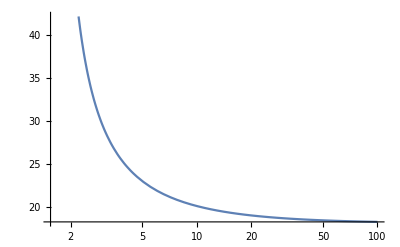

```mathematica
LogLinearPlot[kapBarbLim[wSimple[T,kappa],vb[dPhi],kappa],{kappa,1.55,100}]
```

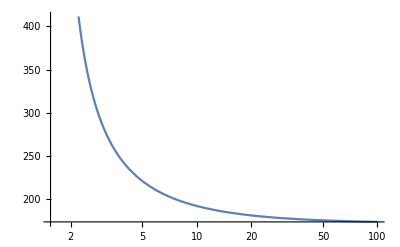

```mathematica
LogLinearPlot[kapBarbLim[wSimple[T,kappa],vb[dPhi*10],kappa],{kappa,1.55,100}]
```

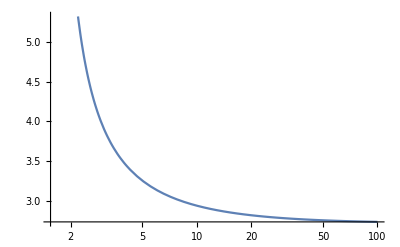

```mathematica
LogLinearPlot[kapBarbLim[wSimple[T,kappa],vb[dPhi/10],kappa],{kappa,1.55,100}]
```

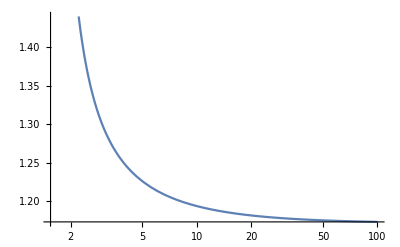

```mathematica
LogLinearPlot[kapBarbLim[wSimple[T,kappa],vb[dPhi/100],kappa],{kappa,1.55,100}]
```

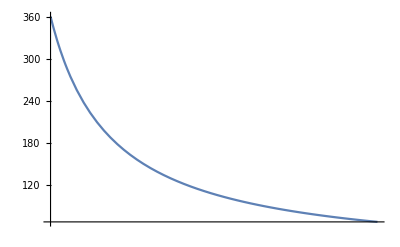

```mathematica
LogLinearPlot[kapBarbLim[wSimple[T,kappa],vb[dPhi],kappa],{kappa,1.55,1.85}]
```

For comparison, the asymptotic Barbosa:

```mathematica
barbAsymp[dPhi,T]
```

18.1094

```mathematica
Simplify[Integralzz]
```

1/4 ((2 a^(2+2 kappa) vb (a^2+vb^2)^-kappa)/kappa+(a^3 √π Gamma[-1/2+kappa])/Gamma[1+kappa]+2 vb^2 ((a √π Gamma[1/2+kappa])/Gamma[1+kappa]+2 vb Hypergeometric2F1[1/2,1+kappa,3/2,-vb^2/a^2])+1/((-1+4 kappa^2) (a^2+vb^2))2 ⅇ^(ⅈ kappa π) (-1-a^2/vb^2)^-kappa vb^(-1-2 kappa) (a^(2+2 kappa) (a^4-8 a^2 kappa vb^2-(1+2 kappa)^2 vb^4)-a^2 (a^2+vb^2)^kappa (a^4+2 a^2 (1-2 kappa) vb^2+(1-4 kappa^2) vb^4) Hypergeometric2F1[-1/2,1+kappa,1/2,-vb^2/a^2]+(1+2 kappa) vb^2 (a^2+vb^2)^kappa (3 a^4-4 a^2 (-1+kappa) vb^2+(1-4 kappa^2) vb^4) Hypergeometric2F1[1/2,1+kappa,3/2,-vb^2/a^2]))